```mathematica
Clear["Global`*"];
```

```mathematica
intensityPeak[power_,waist_]:=(2*power)/(Pi*waist^2);
```

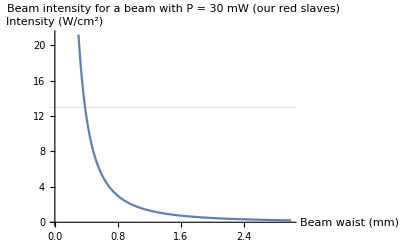
-Graphics-The intensity is calculated according to I=(2*P)/(π*SuperscriptBox[w, 2]). The horizontal line denotes the intensity damage threshold for the quoted Thorlabs optical isolators

```mathematica
plt1=Labeled[Plot[intensityPeak[30*10^-3,beamwaist/10],{beamwaist,0.3,3},PlotLabel->"Beam intensity for a beam with P = 30 mW (our red slaves)",AxesLabel->{"Beam waist (mm)","Intensity (W/cm^2)"},PlotRange->Full,AxesOrigin->{0,0},GridLines->{{0}, {13}}],"The intensity is calculated according to I=(2*P)/(π*SuperscriptBox[w, 2]). The horizontal line denotes the intensity damage threshold for the quoted Thorlabs optical isolators"]
```

```mathematica
(*Export[NotebookDirectory[]<>"redslaveintensity.pdf",plt1]*)
```

Q:\groups\strontium\Oleksiy\Beams and imaging\redslaveintensity.pdf